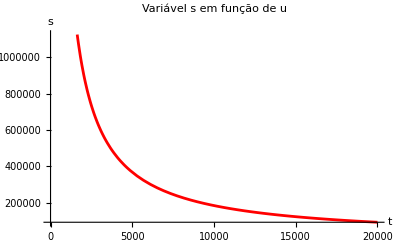

```mathematica
m = 1; (* massa do elétron *)
M = 207*m; (* massa do múon *)

K = 2m^2 + 2M^2;
s[t_] = (M^2 - m^2)^2 / t;

Plot[s[x], {x,0,20000}, AxesLabel ->{"t", "s"}, PlotLabel ->"Variável s em função de u", PlotStyle->{Red}]
```